## DelaunayMean-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 19:01:28
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate 100 random points and their Delaunay Triangulation

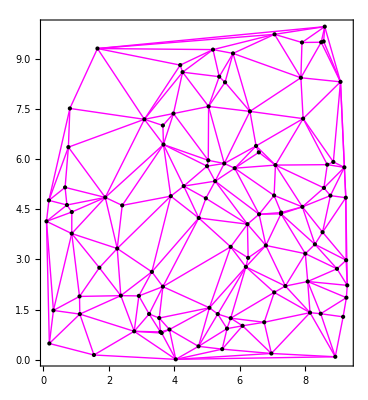

```mathematica
r:=RandomReal[{0, 10}]; 
v=Table[{r,r}, {100}];
de=DelaunayEdges[v];
Show[Graphics[{Magenta,Line/@de}], Graphics[Point/@v] , Frame-> True]
```

```mathematica
DelaunayMean[v]
```

1.19966